```mathematica
<<MaTeX`
```

```mathematica
Pade approximant for the IFM
```

approximant for IFM Pade the

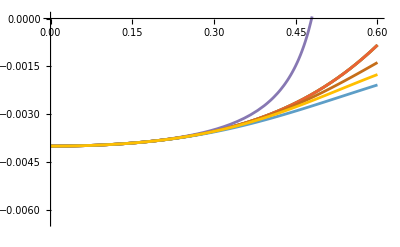

./pade_IFM.pdf

```mathematica
Module[{R, Hlr, Wlr2, Llr2, Mlr2, Wlr3, Wlr4},
R=0;
Hlr=-0.4002*(10)^(-2);
Wlr2=0.01642*(10)^(-3);
Llr2=-0.0829*10^(-4);
Mlr2=0.073*10^(-3);
Wlr3=-0.00665*10^(-5);
Wlr4=-0.0309*(10)^(-6);
energyIFM[x_]:=-63/16 x^3 * R + (1-x-61/18 x^2)Hlr - x (Wlr2+Wlr3+Wlr4)-x^2 (152/27 Wlr2 -Llr2+Mlr2);
coeffIFM={Hlr,-Hlr-Wlr2-Wlr3-Wlr4, -61/18 Hlr-152/27Wlr2 + Llr2-Mlr2, -63/16 R};
energyIFM[x_]:=Total[coeffIFM*{1, x^2, x^4, x^6}]
]
pIFM60[x_]:=Evaluate@PadeApproximant[energyIFM[x], {x,0,6,0}]
pIFM51[x_]:=Evaluate@PadeApproximant[energyIFM[x], {x,0,5,1}]
pIFM42[x_]:=Evaluate@PadeApproximant[energyIFM[x], {x,0,4,2}]
pIFM33[x_]:=Evaluate@PadeApproximant[energyIFM[x], {x,0,3,3}]
pIFM24[x_]:=Evaluate@PadeApproximant[energyIFM[x], {x,0,2,4}]
pIFM15[x_]:=Evaluate@PadeApproximant[energyIFM[x], {x,0,1,5}]
pIFM06[x_]:=Evaluate@PadeApproximant[energyIFM[x], {x,0,0,6}]

plt=Plot[{energyIFM[x], pIFM60[x], pIFM51[x], pIFM42[x], pIFM33[x], pIFM24[x], pIFM15[x], pIFM06[x]},{x,0,0.6}, PlotRange->Automatic,PlotLegends->{MaTeX["\\text{Taylor}"],MaTeX["[6/0]"],MaTeX["[5/1]"],MaTeX["[4/2]"],MaTeX["[3/3]"],MaTeX["[2/4]"],MaTeX["[1/5]"],MaTeX["[0/6]"]},  PlotLabel->MaTeX["\\text{Taylor series and Padé approximants for IFM}"], AxesLabel->{MaTeX["\\Omega/V"],MaTeX["\\text{Energy}"]}]
Export["./pade_IFM.pdf", plt]
```

```mathematica
Pade approximant for the Ice AFM
```

AFM approximant for Ice Pade the

```mathematica
Module[{R, Hlr, Wlr2, Llr2, Mlr2, Wlr3, Wlr4},
R=0;
Hlr=3.8722*(10)^(-2);
Wlr2=1.4994*(10)^(-3);
Llr2=-7.5662*10^(-4);
Mlr2=6.66*10^(-3);
Wlr3=5.81*10^(-5);
Wlr4=-5.35*(10)^(-6);
energyAIFM[x_]:=-63/16 x^3 * R + (1-x-61/18 x^2)Hlr - x (Wlr2+Wlr3+Wlr4)-x^2 (152/27 Wlr2 -Llr2+Mlr2);
coeffAIFM={Hlr,-Hlr-Wlr2-Wlr3-Wlr4, -61/18 Hlr-152/27Wlr2 + Llr2-Mlr2, -63/16 R};
energyAIFM[x_]:=Total[coeffAIFM*{1, x^2, x^4, x^6}]
]
pAIFM60[x_]:=Evaluate@PadeApproximant[energyAIFM[x],{x,0,6,0}]
pAIFM51[x_]:=Evaluate@PadeApproximant[energyAIFM[x],{x,0,5,1}]
pAIFM42[x_]:=Evaluate@PadeApproximant[energyAIFM[x],{x,0,4,2}]
pAIFM33[x_]:=Evaluate@PadeApproximant[energyAIFM[x],{x,0,3,3}]
pAIFM24[x_]:=Evaluate@PadeApproximant[energyAIFM[x],{x,0,2,4}]
pAIFM15[x_]:=Evaluate@PadeApproximant[energyAIFM[x],{x,0,1,5}]
pAIFM06[x_]:=Evaluate@PadeApproximant[energyAIFM[x],{x,0,0,6}]

plt=Plot[{energyAIFM[x],pAIFM60[x],pAIFM51[x],pAIFM42[x],pAIFM33[x],pAIFM24[x],pAIFM15[x],pAIFM06[x]},{x,0,0.6},PlotRange->{-0.125,0.05},PlotLabels->{MaTeX["\\text{Taylor}"],MaTeX["[6/0]"],MaTeX["[5/1]"],MaTeX["[4/2]"],MaTeX["[3/3]"],MaTeX["[2/4]"],MaTeX["[1/5]"],MaTeX["[0/6]"]},PlotLabel->MaTeX["\\text{Taylor series and Padé approximants for AIFM}"],AxesLabel->{MaTeX["\\Omega/V"],MaTeX["\\text{Energy}"]}]
Export["./pade_IAFM.pdf", plt]
```

-Graphics-

./pade_IAFM.pdf

```mathematica
Plot[{energyAIFM[x], energyRK[x], energyIFM[x]},{x,0,.6},PlotLabels->{"Ice AFM", "RK", "Ice FM"}, PlotRange->{-0.125, 0.05}]
```

-Graphics-

```mathematica
Pade approximant for the RK
```

approximant for Pade RK the

```mathematica
Module[{R, Hlr, Wlr2, Llr2, Mlr2, Wlr3, Wlr4},
R = 0.702884;
Hlr = 2.60371*10^(-2);
Wlr2 = 1.117781*10^(-3);
Llr2 = -2.74673*10^(-4);
Mlr2 = 2.963*(10)^(-3);
Wlr3=5.254*(10)^(-5);
Wlr4=-3.572*(10)^(-6);
coeffRK={Hlr,-Hlr-Wlr2-Wlr3-Wlr4, -61/18 Hlr-152/27Wlr2 + Llr2-Mlr2, -63/16 R};
energyRK[x_]:=-63/16 x^3 * R + (1-x-61/18 x^2)Hlr - x (Wlr2+Wlr3+Wlr4)-x^2 (152/27 Wlr2 -Llr2+Mlr2);
energyRK[x_]:=Total[coeffRK*{1, x^2, x^4, x^6}]
]
pRK60[x_]:=Evaluate@PadeApproximant[energyRK[x],{x,0,6,0}]
pRK51[x_]:=Evaluate@PadeApproximant[energyRK[x],{x,0,5,1}]
pRK42[x_]:=Evaluate@PadeApproximant[energyRK[x],{x,0,4,2}]
pRK33[x_]:=Evaluate@PadeApproximant[energyRK[x],{x,0,3,3}]
pRK24[x_]:=Evaluate@PadeApproximant[energyRK[x],{x,0,2,4}]
pRK15[x_]:=Evaluate@PadeApproximant[energyRK[x],{x,0,1,5}]
pRK06[x_]:=Evaluate@PadeApproximant[energyRK[x],{x,0,0,6}]

plt=Plot[{energyRK[x],pRK60[x],pRK51[x],pRK42[x],pRK33[x],pRK24[x],pRK15[x],pRK06[x]},{x,0,0.6}, PlotRange->{-0.125, 0.05},PlotLabels->{MaTeX["\\text{Taylor}"],MaTeX["[6/0]"],MaTeX["[5/1]"],MaTeX["[4/2]"],MaTeX["[3/3]"],MaTeX["[2/4]"],MaTeX["[1/5]"],MaTeX["[0/6]"]},PlotLabel->MaTeX["\\text{Taylor series and Padé approximants for RK}"],AxesLabel->{MaTeX["\\Omega/V"],MaTeX["\\text{Energy}"]}]
Export["./pade_RK.pdf",plt]
```

-Graphics-

./pade_RK.pdf

```mathematica
Borel-Pade approximant for the RK
```

Borel-approximant for Pade RK the

```mathematica
Module[{R, Hlr, Wlr2, Llr2, Mlr2, Wlr3, Wlr4},
R = 0.702884;
Hlr = 2.60371*10^(-2);
Wlr2 = 1.117781*10^(-3);
Llr2 = -2.74673*10^(-4);
Mlr2 = 2.963*(10)^(-3);
Wlr3=5.254*(10)^(-5);
Wlr4=-3.572*(10)^(-6);
coeffRK={Hlr,-Hlr-Wlr2-Wlr3-Wlr4, -61/18 Hlr-152/27Wlr2 + Llr2-Mlr2, -63/16 R};
energyRK[x_]:=-63/16 x^3 * R + (1-x-61/18 x^2)Hlr - x (Wlr2+Wlr3+Wlr4)-x^2 (152/27 Wlr2 -Llr2+Mlr2);
energyRK[x_]:=Total[coeffRK*{1, x^2, x^4, x^6}];
borelRK[x_]:=Total[coeffRK*{0, x, x^3/Factorial[3], x^5/Factorial[5]}]
]
(*pbRK06[x_]:=Evaluate@PadeApproximant[borelRK[x], {x,0,0,6}]
pblRK06[t_]:=energyRK[0]+NIntegrate[pbRK06[x] Exp[-x/t],{x,0,Infinity}]*)

pbRK15[x_]:=Evaluate@PadeApproximant[borelRK[x], {x,0,1,5}]
pblRK15[t_]:=energyRK[0]+NIntegrate[pbRK15[x] Exp[-x/t],{x,0,Infinity}]

pbRK24[x_]:=Evaluate@PadeApproximant[borelRK[x], {x,0,2,4}]
pblRK24[t_]:=energyRK[0]+NIntegrate[pbRK24[x] Exp[-x/t],{x,0,Infinity}]

pbRK33[x_]:=Evaluate@PadeApproximant[borelRK[x], {x,0,3,3}]
pblRK33[t_]:=energyRK[0]+NIntegrate[pbRK33[x] Exp[-x/t],{x,0,Infinity}]

pbRK42[x_]:=Evaluate@PadeApproximant[borelRK[x], {x,0,4,2}]
pblRK42[t_]:=energyRK[0]+NIntegrate[pbRK42[x] Exp[-x/t],{x,0,Infinity}]

pbRK51[x_]:=Evaluate@PadeApproximant[borelRK[x], {x,0,5,1}]
pblRK51[t_]:=energyRK[0]+NIntegrate[pbRK51[x] Exp[-x/t],{x,0,Infinity}]

pbRK60[x_]:=Evaluate@PadeApproximant[borelRK[x], {x,0,6,0}]
pblRK60[t_]:=energyRK[0]+NIntegrate[pbRK60[x] Exp[-x/t],{x,0,Infinity}]

(*pRK21[x_]:=Evaluate@PadeApproximant[energyRK[x], {x,0,2,1}]
pRK30[x_]:=Evaluate@PadeApproximant[energyRK[x], {x,0,3,0}]
pRK03[x_]:=Evaluate@PadeApproximant[energyRK[x], {x,0,0,3}]
*)
plt=Plot[{energyRK[x], pblRK15[x], pblRK24[x], pblRK33[x], pblRK42[x], pblRK51[x], pblRK60[x]},{x,0,0.6}, PlotRange->{-0.125, 0.05},PlotLabels->{"Taylor","[1/5]","[2/4]","[3/3]","[4/2]","[5/1]","[6/0]"}, PlotLabel->MaTeX["\\text{Borel-Padé approximants for RK ansatz}"], AxesLabel->{MaTeX["\\frac{\\Omega}{V}"], MaTeX["\\frac{\\langle \\hat{H}_\\text{eff} \\rangle}{ N_\\text{u.c.} V}"]}]
(*Export[NotebookDirectory[]<>"./borel_pade_RK.pdf",plt]*)
```

-Graphics-

/Users/jeet/umd/acad/projects/quantum_spin_ice_rydbergs/numerics/./borel_pade_RK.pdf

```mathematica
Borel-Pade approximant for the IFM
```

Borel-approximant for IFM Pade the

```mathematica
Module[{R,Hlr,Wlr2,Llr2,Mlr2,Wlr3,Wlr4},R=0;
Hlr=-0.4002*(10)^(-2);
Wlr2=0.01642*(10)^(-3);
Llr2=-0.0829*10^(-4);
Mlr2=0.073*10^(-3);
Wlr3=-0.00665*10^(-5);
Wlr4=-0.0309*(10)^(-6);
coeffIFM={Hlr,-Hlr-Wlr2-Wlr3-Wlr4,-61/18 Hlr-152/27 Wlr2+Llr2-Mlr2,-63/16 R};
energyIFM[x_]:=-63/16 x^3*R+(1-x-61/18 x^2) Hlr-x (Wlr2+Wlr3+Wlr4)-x^2 (152/27 Wlr2-Llr2+Mlr2);
energyIFM[x_]:=Total[coeffIFM*{1,x^2,x^4,x^6}];

borelIFM[x_]:=Total[coeffIFM*{0,x,x^3/Factorial[3],x^5/Factorial[5]}]]

(*pbIFM06[x_]:=Evaluate@PadeApproximant[borelIFM[x],{x,0,0,6}] 
pblIFM06[t_]:=energyIFM[0]+NIntegrate[pbIFM06[x] Exp[-x/t],{x,0,Infinity}]*)

pbIFM15[x_]:=Evaluate@PadeApproximant[borelIFM[x],{x,0,1,5}]
pblIFM15[t_]:=energyIFM[0]+NIntegrate[pbIFM15[x]  Exp[-x/t],{x,0,Infinity}]

pbIFM24[x_]:=Evaluate@PadeApproximant[borelIFM[x],{x,0,2,4}]
pblIFM24[t_]:=energyIFM[0]+NIntegrate[pbIFM24[x]  Exp[-x/t],{x,0,Infinity}]

pbIFM33[x_]:=Evaluate@PadeApproximant[borelIFM[x],{x,0,3,3}]
pblIFM33[t_]:=energyIFM[0]+NIntegrate[pbIFM33[x]  Exp[-x/t],{x,0,Infinity}]

pbIFM42[x_]:=Evaluate@PadeApproximant[borelIFM[x],{x,0,4,2}]
pblIFM42[t_]:=energyIFM[0]+NIntegrate[pbIFM42[x]  Exp[-x/t],{x,0,Infinity}]

pbIFM51[x_]:=Evaluate@PadeApproximant[borelIFM[x],{x,0,5,1}]
pblIFM51[t_]:=energyIFM[0]+NIntegrate[pbIFM51[x]  Exp[-x/t],{x,0,Infinity}]

pbIFM60[x_]:=Evaluate@PadeApproximant[borelIFM[x],{x,0,6,0}]
pblIFM60[t_]:=energyIFM[0]+NIntegrate[pbIFM60[x]  Exp[-x/t],{x,0,Infinity}]


plt=Plot[{energyIFM[x],pblIFM15[x],pblIFM24[x],pblIFM33[x],pblIFM42[x],pblIFM51[x],pblIFM60[x]},{x,0,0.6},PlotRange->Automatic,PlotLabels->{"Taylor","[1/5]","[2/4]","[3/3]","[4/2]","[5/1]","[6/0]"},PlotLabel->MaTeX["\\text{Borel-Padé approximants for ice FM}"],AxesLabel->{MaTeX["\\frac{\\Omega}{V}"],MaTeX["\\frac{\\langle \\hat{H}_\\text{eff} \\rangle}{ N_\\text{u.c.} V}"]}]
(*Export[NotebookDirectory[]<>"borel_pade_IFM.pdf",plt]*)
```

-Graphics-

/Users/jeet/umd/acad/projects/quantum_spin_ice_rydbergs/numerics/borel_pade_IFM.pdf

```mathematica
Borel-Pade approximant for the Ice AFM
```

Borel-AFM approximant for Ice Pade the

```mathematica
Module[{R,Hlr,Wlr2,Llr2,Mlr2,Wlr3,Wlr4},
R=0;
Hlr=3.8722*(10)^(-2);
Wlr2=1.4994*(10)^(-3);
Llr2=-7.5662*10^(-4);
Mlr2=6.66*10^(-3);
Wlr3=5.81*10^(-5);
Wlr4=-5.35*(10)^(-6);
coeffIAFM={Hlr,-Hlr-Wlr2-Wlr3-Wlr4,-61/18  Hlr-152/27  Wlr2+Llr2-Mlr2,-63/16  R};
energyIAFM[x_]:=-63/16  x^3*R+(1-x-61/18  x^2)  Hlr-x  (Wlr2+Wlr3+Wlr4)-x^2  (152/27  Wlr2-Llr2+Mlr2);
energyIAFM[x_]:=Total[coeffIAFM*{1,x^2,x^4,x^6}];
borelIAFM[x_]:=Total[coeffIAFM*{0,x,x^3/Factorial[3],x^5/Factorial[5]}]]

(*pbIAFM06[x_]:=Evaluate@PadeApproximant[borelIAFM[x],{x,0,0,6}] pblIAFM06[t_]:=energyIAFM[0]+NIntegrate[pbIAFM06[x] Exp[-x/t],{x,0,Infinity}]*)

pbIAFM15[x_]:=Evaluate@PadeApproximant[borelIAFM[x],{x,0,1,5}]
pblIAFM15[t_]:=energyIAFM[0]+NIntegrate[pbIAFM15[x]   Exp[-x/t],{x,0,Infinity}]

pbIAFM24[x_]:=Evaluate@PadeApproximant[borelIAFM[x],{x,0,2,4}]
pblIAFM24[t_]:=energyIAFM[0]+NIntegrate[pbIAFM24[x]   Exp[-x/t],{x,0,Infinity}]

pbIAFM33[x_]:=Evaluate@PadeApproximant[borelIAFM[x],{x,0,3,3}]
pblIAFM33[t_]:=energyIAFM[0]+NIntegrate[pbIAFM33[x]   Exp[-x/t],{x,0,Infinity}]

pbIAFM42[x_]:=Evaluate@PadeApproximant[borelIAFM[x],{x,0,4,2}]
pblIAFM42[t_]:=energyIAFM[0]+NIntegrate[pbIAFM42[x]   Exp[-x/t],{x,0,Infinity}]

pbIAFM51[x_]:=Evaluate@PadeApproximant[borelIAFM[x],{x,0,5,1}]
pblIAFM51[t_]:=energyIAFM[0]+NIntegrate[pbIAFM51[x]   Exp[-x/t],{x,0,Infinity}]

pbIAFM60[x_]:=Evaluate@PadeApproximant[borelIAFM[x],{x,0,6,0}]
pblIAFM60[t_]:=energyIAFM[0]+NIntegrate[pbIAFM60[x]   Exp[-x/t],{x,0,Infinity}]


plt=Plot[{energyIAFM[x],pblIAFM15[x],pblIAFM24[x],pblIAFM33[x],pblIAFM42[x],pblIAFM51[x],pblIAFM60[x]},{x,0,0.6},PlotRange->Automatic,PlotLabels->{"Taylor","[1/5]","[2/4]","[3/3]","[4/2]","[5/1]","[6/0]"},PlotLabel->MaTeX["\\text{Borel-Padé approximants for ice AFM}"],AxesLabel->{MaTeX["\\frac{\\Omega}{V}"],MaTeX["\\frac{\\langle \\hat{H}_\\text{eff} \\rangle}{ N_\\text{u.c.} V}"]}]
(*Export[NotebookDirectory[]<>"./borel_pade_IAFM.pdf",plt]*)
```

-Graphics-

/Users/jeet/umd/acad/projects/quantum_spin_ice_rydbergs/numerics/./borel_pade_IAFM.pdf

```mathematica
Borel-Pade approximant for the RK

Module[{R,Hlr,Wlr2,Llr2,Mlr2,Wlr3,Wlr4},
R=0.702884;
Hlr=10^(-8);
Wlr2=10^(-8);
Llr2=10^(-8);
Mlr2=10^(-8);
Wlr3=10^(-8);
Wlr4=10^(-8);
coeffABC={Hlr,-Hlr-Wlr2-Wlr3-Wlr4,-61/18  Hlr-152/27 Wlr2+Llr2-Mlr2,-63/16  R};
energyABC[x_]:=-63/16  x^3*R+(1-x-61/18  x^2) Hlr-x  (Wlr2+Wlr3+Wlr4)-x^2  (152/27  Wlr2-Llr2+Mlr2);
energyABC[x_]:=Total[coeffABC*{1,x^2,x^4,x^6}];
borelABC[x_]:=Total[coeffABC*{0,x,x^3/Factorial[3],x^5/Factorial[5]}]]
(*pbABC06[x_]:=Evaluate@PadeApproximant[borelABC[x],{x,0,0,6}] pblABC06[t_]:=energyABC[0]+NIntegrate[pbABC06[x] Exp[-x/t],{x,0,Infinity}]*)

pbABC15[x_]:=Evaluate@PadeApproximant[borelABC[x],{x,0,1,5}]
pblABC15[t_]:=energyABC[0]+NIntegrate[pbABC15[x]  Exp[-x/t],{x,0,Infinity}]

pbABC24[x_]:=Evaluate@PadeApproximant[borelABC[x],{x,0,2,4}]
pblABC24[t_]:=energyABC[0]+NIntegrate[pbABC24[x]  Exp[-x/t],{x,0,Infinity}]

pbABC33[x_]:=Evaluate@PadeApproximant[borelABC[x],{x,0,3,3}]
pblABC33[t_]:=energyABC[0]+NIntegrate[pbABC33[x]  Exp[-x/t],{x,0,Infinity}]

pbABC42[x_]:=Evaluate@PadeApproximant[borelABC[x],{x,0,4,2}]
pblABC42[t_]:=energyABC[0]+NIntegrate[pbABC42[x]  Exp[-x/t],{x,0,Infinity}]

pbABC51[x_]:=Evaluate@PadeApproximant[borelABC[x],{x,0,5,1}]
pblABC51[t_]:=energyABC[0]+NIntegrate[pbABC51[x]  Exp[-x/t],{x,0,Infinity}]

pbABC60[x_]:=Evaluate@PadeApproximant[borelABC[x],{x,0,6,0}]
pblABC60[t_]:=energyABC[0]+NIntegrate[pbABC60[x]  Exp[-x/t],{x,0,Infinity}]

(*pABC21[x_]:=Evaluate@PadeApproximant[energyABC[x],{x,0,2,1}] pABC30[x_]:=Evaluate@PadeApproximant[energyABC[x],{x,0,3,0}] pABC03[x_]:=Evaluate@PadeApproximant[energyABC[x],{x,0,0,3}]*)
plt=Plot[{energyABC[x],pblABC15[x],pblABC24[x],pblABC33[x],pblABC42[x],pblABC51[x],pblABC60[x]},{x,0,0.6},PlotRange->{-0.125,0.05},PlotLabels->{"Taylor","[1/5]","[2/4]","[3/3]","[4/2]","[5/1]","[6/0]"},PlotLabel->MaTeX["\\begin{aligned}  \\text{Borel-} & \\text{Padé approximants for RK with} \\\\ & \\text{no long-range interactions} \\end{aligned}"],AxesLabel->{MaTeX["\\frac{\\Omega}{V}"],MaTeX["\\frac{\\langle \\hat{H}_\\text{eff} \\rangle}{ N_\\text{u.c.} V}"]}]
Export[NotebookDirectory[]<>"./borel_pade_RK_noLR.pdf",plt]
```

Borel-approximant for Pade RK the

-Graphics-

/Users/jeet/umd/acad/projects/quantum_spin_ice_rydbergs/numerics/./borel_pade_RK_noLR.pdf

```mathematica
Transition point
```

point Transition

```mathematica
Solve[energyIFM[x] == energyRK[x], x]
```

{{x→-0.439266},{x→-0.245574-0.420554 ⅈ},{x→-0.245574+0.420554 ⅈ},{x→0.245574-0.420554 ⅈ},{x→0.245574+0.420554 ⅈ},{x→0.439266}}

```mathematica
Solve[energyRK[x] == pblIFM24[x], x]
```

{{x→-0.433307},{x→-0.240693-0.411672 ⅈ},{x→-0.240693+0.411672 ⅈ},{x→0.240693-0.411672 ⅈ},{x→0.240693+0.411672 ⅈ},{x→0.433307}}

```mathematica
{{x->-0.43330739196544044},{x->-0.24069345596951564-0.41167191360497796 ⅈ},{x->-0.24069345596951564+0.41167191360497796 ⅈ},{x->0.24069345596951564-0.41167191360497796 ⅈ},{x->0.24069345596951564+0.41167191360497796 ⅈ},{x->0.43330739196544044}}
```

{{x→-0.433307},{x→-0.240693-0.411672 ⅈ},{x→-0.240693+0.411672 ⅈ},{x→0.240693-0.411672 ⅈ},{x→0.240693+0.411672 ⅈ},{x→0.433307}}

```mathematica
{{x->-0.5998051559537049},{x->0.-0.8108378322712655 ⅈ},{x->0.+0.8108378322712655 ⅈ},{x->0.5998051559537049}}
```

{{x→-0.599805},{x→0.-0.810838 ⅈ},{x→0.+0.810838 ⅈ},{x→0.599805}}

```mathematica
y =0.44067;
(energyRK[y]- pblIFM24[y])/energyRK[y]
```

-0.0000407881

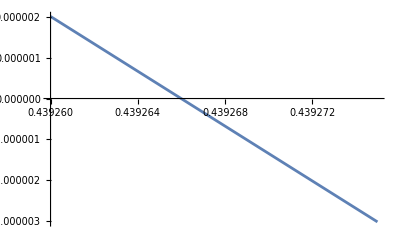

```mathematica
Plot[{ energyRK[x] - energyIFM[x]},{x,0.43926,0.439275}]
```

0.44067

-0.174866

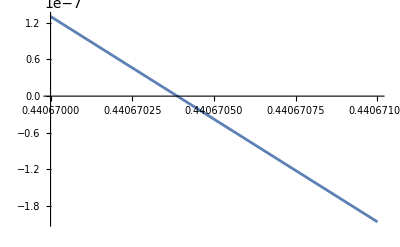

```mathematica
ωcNew = 0.44067
(energyIFM[ωcNew]- pblIFM24[ωcNew])/energyIFM[ωcNew]
Plot[{energyRK[x] - pblIFM24[x]},{x,0.440670,0.440671}]
```

```mathematica
(energyIAFM[ωcNew]- pblIAFM24[ωcNew])/pblIAFM24[ωcNew]
```

-0.17463

```mathematica
energyRK[x]
```

0.0260371-0.0272038 x^2-0.0977672 x^4-2.76761 x^6

```mathematica
energyABC[x]
```

1/100000000-x^2/25000000-(487 x^4)/5400000000-2.76761 x^6

```mathematica
Simplify[1/100000000-x^2/25000000-(487 x^4)/5400000000-2.76760575 x^6]
```

1.×10^-8-4.×10^-8 x^2-9.01852×10^-8 x^4-2.76761 x^6

```mathematica
pblABC24[x]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.0369732}. NIntegrate obtained -2.89368×10^-11 and 3.31348×10^-11 for the integral and error estimates.

9.97106×10^-9

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {3.15019×10^-6}. NIntegrate obtained -6.343×10^-18 and 2.18424×10^-20 for the integral and error estimates.

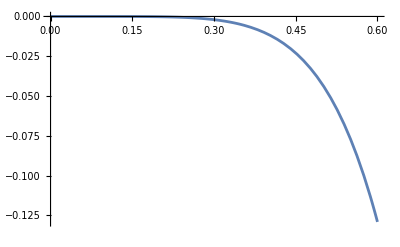

```mathematica
pbABC[x_]:=Evaluate@PadeApproximant[borelABC[x],{x,4,8,0}]
pblABC[t_]:=energyABC[0]+NIntegrate[pbABC[x]  Exp[-x/t],{x,0,Infinity}]
Plot[pblABC[x], {x,0,0.6}]
```

```mathematica
energyRK[x]
```

0.0260371-0.0272038 x^2-0.0977672 x^4-2.76761 x^6

```mathematica
energyIFM[x]
```

-0.004002+0.00398568 x^2+0.0133886 x^4

```mathematica
energyAIFM[x]
```

0.038722-0.0402741 x^2-0.147082 x^4

```mathematica
2.7/0.0977
```

27.6356

```mathematica
0.0133/0.00398
```

3.34171

```mathematica
0.147/0.0402
```

3.65672

```mathematica
energyRK[ωc]*{0.8,1.2}
```

{0.8 (0.0260371-0.0272038 ωc^2-0.0977672 ωc^4-2.76761 ωc^6),1.2 (0.0260371-0.0272038 ωc^2-0.0977672 ωc^4-2.76761 ωc^6)}

```mathematica
energyIFM[ωc]*{0.8,1.2}
```

{0.8 (-0.004002+0.00398568 ωc^2+0.0133886 ωc^4),1.2 (-0.004002+0.00398568 ωc^2+0.0133886 ωc^4)}

```mathematica
energyRK[]
```

energyRK[]

```mathematica
energyRK[x]
```

0.0260371-0.0272038 x^2-0.0977672 x^4-2.76761 x^6

```mathematica
0.0260371/2.76760575
```

0.00940781

```mathematica
1/0.00940781
```

106.295

```mathematica
2.76760575/0.09776720492592593
```

28.3081

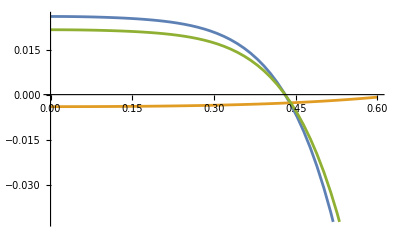

```mathematica
Plot[{energyRK[x], energyIFM[x], 0.83energyRK[x]}, {x,0,0.6}]
```